# Notebook 03: Randomness

## William J Turkel, wturkel@uwo.ca Digital Humanities 1011B

## Random integers

We can use the RandomInteger command to give us a number between 0 and 99 as follows. Every time we evaluate the command, we will get a different result

```mathematica
RandomInteger[99]
```

39

We can generate a pair of random integers (each between 0 and 99) with the following command

```mathematica
RandomInteger[99,2]
```

{54,7}

We can use the Table command to generate a list of 20 such pairs of numbers as follows

```mathematica
Table[RandomInteger[99,2],{20}]
```

{{19,83},{40,4},{12,79},{41,25},{12,63},{57,79},{71,85},{48,58},{49,81},{86,66},{61,91},{50,85},{44,43},{3,26},{98,96},{74,43},{14,84},{4,3},{19,17},{73,14}}

## Drawing a starry sky

We can use randomness like this to draw a starry sky. First we make a black rectangle for space.

```mathematica
sky={Black,Rectangle[{0,0},{100,100}]};
```

Then we make a function that draws a number of stars. We can tell the function how many stars we want to draw.

```mathematica
drawStars[n_]:=
{LightGray,PointSize[Medium],Point[Table[RandomInteger[99,2],{n}]]}
```

Here is a sky with 15 stars.

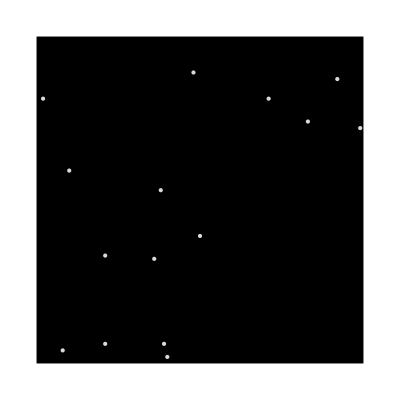

```mathematica
Graphics[Join[sky,drawStars[15]]]
```

Here is a sky with 100 stars.

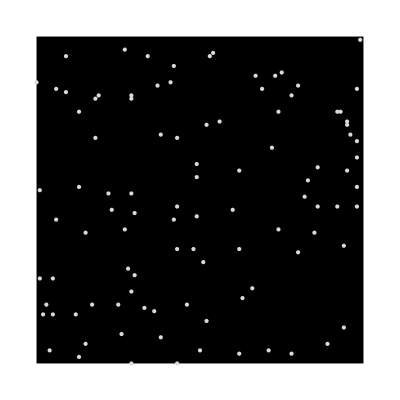

```mathematica
Graphics[Join[sky,drawStars[100]]]
```

## The RandomChoice command

The RandomChoice command randomly returns an element from a list. Here is how we choose either Black or Yellow randomly, with equal probability of choosing either.

```mathematica
RandomChoice[{Black,Yellow}]
```

GrayLevel[0]

We will actually want Black to be more likely than Yellow, so we weight the probabilities so that Black occurs 80% of the time.

```mathematica
RandomChoice[{4/5,1/5}->{Black,Yellow}]
```

GrayLevel[0]

We can create 100 examples to see that Yellow occurs approximately 20% of the time

```mathematica
Table[RandomChoice[{4/5,1/5}->{Black,Yellow}],{100}]
```

{GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0],GrayLevel[0]}

## Mixing random and non-random elements

Let’s add a cityscape along the bottom of our picture of a starry night. We will do this in stages. First we are going to design a repeatable element that is a section of wall with a window. Then we are going to stack up a number of these wall sections to create buildings. Finally, we will draw a row of buildings to make the city scape. At each stage, we will combine both random and non-random elements.

### A section of wall

To draw a section of wall, we are going to make a grey rectangle, then place either a black or yellow smaller rectangle on top of it. (This will be the window, which is either dark or lit up). We will provide x and y coordinates so we can draw copies of the wall segment in arbitrary locations. The origin for our relative coordinates is the lower left hand corner of the wall section.

```mathematica
drawWall[{x_,y_}]:=
{Gray,Rectangle[{x,y},{x+5,y+5}],RandomChoice[{4/5,1/5}->{Black,Yellow}],Rectangle[{x+1,y+1},{x+4,y+4}]}
```

Here is what our wall section looks like. Each time we re-evaluate the cell, it will randomly choose a Black or Yellow window. Black is much more common.

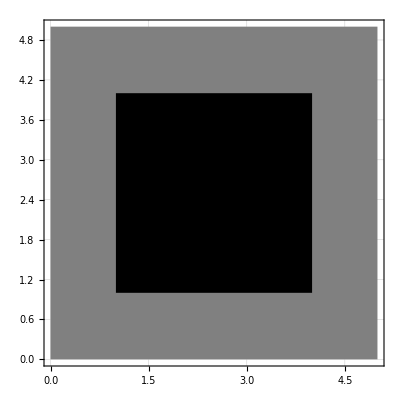

```mathematica
Graphics[drawWall[{0,0}],GridLines->Automatic,Frame->True]
```

### A building

To draw a building, we will make a stack of wall sections that is between 2 and 8 elements high. We will provide x and y coordinates so we can draw buildings in arbitrary locations. The origin for our relative coordinates is the lower left hand corner of the building.

```mathematica
drawBuilding[{x_,y_}]:=
Table[drawWall[{x,s*5}],{s,0,RandomInteger[6]+1}]
```

Here is what a random building looks like

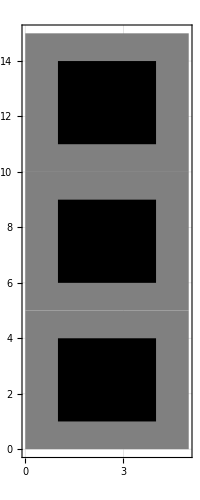

```mathematica
Graphics[drawBuilding[{0,0}],GridLines->Automatic,Frame->True]
```

### The Table command we used

In the function above, we used a somewhat complicated Table command. The value s (for ‘storeys’) counts up from 0 to some upper limit, which is set by RandomInteger[6] + 1. Since the random part of the expression can range from 0 to 6, the upper limit can range from 1 to 7. Since we are counting from 0, if we count 0-1 we have two elements, 0-1-2, three elements, and so on, up to 0-1-2-3-4-5-6-7, which is eight elements. Each time we evaluate the function, we get a new upper limit, and thus a new Table command. When we draw the wall sections, we have to multiply s by 5 because each storey is 5 units high. The x coordinate, which sets the left edge of each wall section, doesn’t change, because we want the wall sections to stack on top of one another.

### The Cityscape

To generate a cityscape, we need to draw a row of buildings. Each building is 5 units wide, and our overall picture is 100 units wide, so we need to draw 20 buildings (i.e., 100 / 5). The x coordinate of each of these buildings has to start at 0 and increase by 5 units for each building (so they draw from left to right), but the y coordinate will always be 0 (so they form a row along the bottom edge of the picture).

```mathematica
drawCity[]:=
Table[drawBuilding[{x,0}],{x,0,95,5}]
```

Here is a cityscape with the coordinates shown.

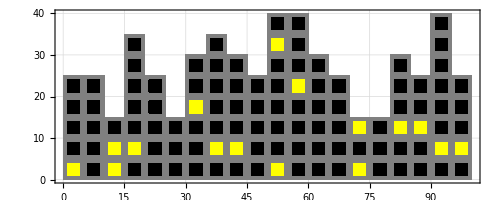

```mathematica
Graphics[Table[drawBuilding[{x,0}],{x,0,95,5}],GridLines->Automatic,Frame->True]
```

Here is our image with the cityscape included.

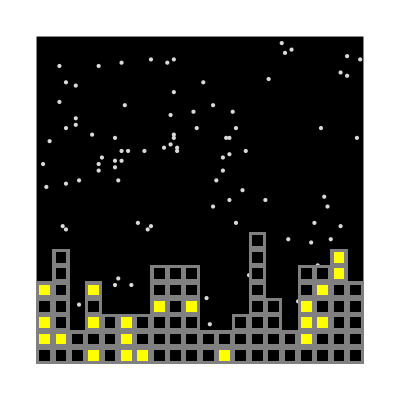

```mathematica
Graphics[Join[sky,drawStars[100],drawCity[]]]
```

Why did we count from 0 to 95 in the Table command above, rather than 0 to 100?

## Drawing a moon

We can use random integers to specify the centre coordinates or radius of a circle, or both.

### The background disk

Suppose we want to draw a moon. We can start with a white Disk of radius 20. We want to draw the moon after we draw our stars, so it appears in front of them. Let’s try centring it at {30, 70} to see how it looks.

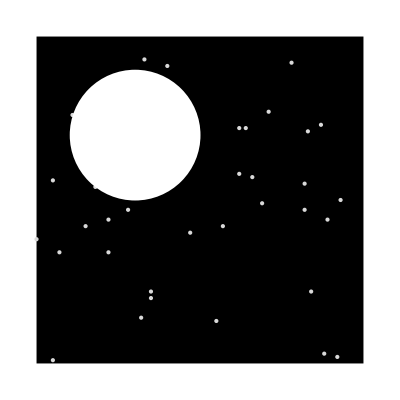

```mathematica
Graphics[Join[sky,drawStars[40],{White,Disk[{30,70},20]}]]
```

### Relative coordinates

Now we want to make a moon-drawing function that uses relative coordinates. This is what we have so far:

drawMoon[{x_, y_}] :=
 {White, Disk[{x, y}, 20]}

### Craters: radius

To add craters, we are going to draw some smaller, randomly-placed light grey circles on top of the moon. We use both random centre position and random radius for each crater.

We want our craters to be small, so we set the radius of each to a random integer between 1 and 4. Recall that RandomInteger[3] returns a value between 0 and 3. To get a value between 1 and 4, we have to add one to the output, like this:

```mathematica
RandomInteger[3]+1
```

2

### Craters: centre coordinates

The centre coordinates for the craters are more tricky. The centre of the moon is {0, 0} and the radius is 20. That means that our moon sits inside a rectangle with relative coordinates {-20, -20} to {20, 20}. We can try drawing the moon and the rectangle surrounding it to see this:

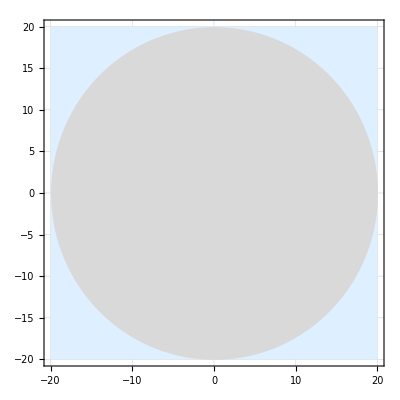

```mathematica
Graphics[{LightBlue,Rectangle[{-20,-20},{20,20}],LightGray,Disk[{0,0},20]},GridLines->Automatic,Frame->True]
```

We can generate coordinates in the range -20 to 20 with a command like

```mathematica
{RandomInteger[40]-20,RandomInteger[40]-20}
```

{-9,-14}

But if we put craters in those locations, some of them will fall inside the rectangle, but outside the circumference of the moon. We can see this by plotting 100 random points over the top of our moon / rectangle image.

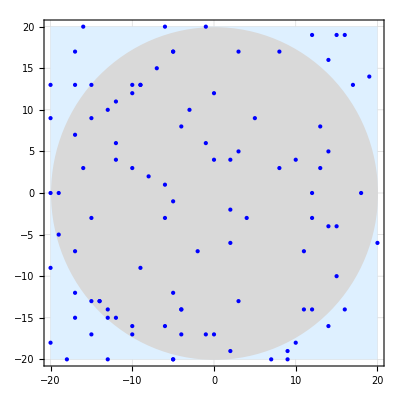

```mathematica
Graphics[{LightBlue,Rectangle[{-20,-20},{20,20}],LightGray,Disk[{0,0},20],PointSize[Medium],Blue,Point[Table[{RandomInteger[40]-20,RandomInteger[40]-20},{100}]]},GridLines->Automatic,Frame->True]
```

We could get a nice solution to our problem using trigonometry, but for now we will just force the centre coordinates of each crater to be within the range of -11 to 11 with a command like

```mathematica
{RandomInteger[22]-11,RandomInteger[22]-11}
```

{2,10}

Here are 100 such random coordinate pairs plotted over the moon / rectangle image. Notice that they fall inside a rectangle which has relative coordinates {-11, -11} to {11, 11}.

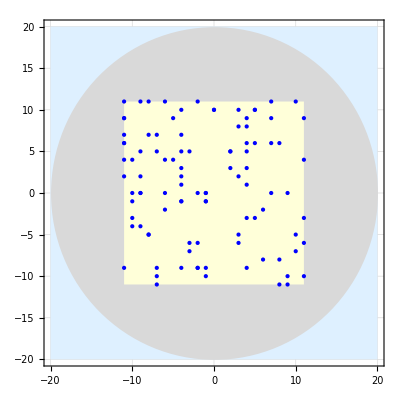

```mathematica
Graphics[{LightBlue,Rectangle[{-20,-20},{20,20}],LightGray,Disk[{0,0},20],LightYellow, Rectangle[{-11,-11},{11,11}],PointSize[Medium],Blue,Point[Table[{RandomInteger[22]-11,RandomInteger[22]-11},{100}]]},GridLines->Automatic,Frame->True]
```

### Drawing the moon

Given that, here is our moon-drawing function. It draws 8 craters.

```mathematica
drawMoon[{x_,y_}]:=
{White,Disk[{x,y},20],LightGray,Table[Circle[{x+(RandomInteger[22]-11),y+(RandomInteger[22]-11)},RandomInteger[3]+1],{8}]}
```

### The final picture

Here is our final version, with the stars, moon and the cityscape:

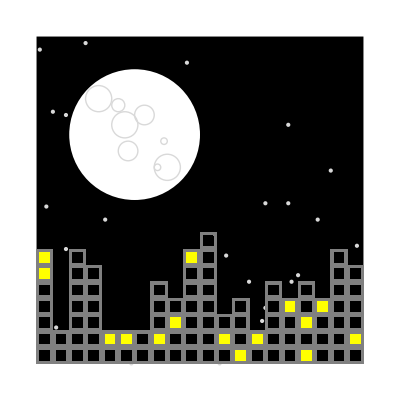

```mathematica
Graphics[Join[sky,drawStars[40],drawMoon[{30,70}],drawCity[]]]
```

## In-Class Activity

### Draw a picture using the Graphics command. Use a mixture of random and non-random coordinates to place objects in the scene (e.g., trees, snowflakes, clouds, cars, people, etc.)

#### NAME:

#### STUDENT NUMBER:

#### DATE:

## Upload your notebook

Don’t forget to upload a copy of your notebook for this day’s class to the OWL Site for the course